```mathematica
SetDirectory ["/Volumes/MicroSD/Dropbox/PostDoc_SD/mathematica/ZrC_analysis/MD-trajectory"];
filePDF={"pdf-Frenkel_500_222kp-6hr-9.700-46hrRERUN.m","pdf-Frenkel_500_222kp-6hr-9.370.m"};
dataPDF= Table[ReadList[filePDF[[i]],Table[Number,{i,1,5}]],{i,1,Length[filePDF]}];
```

```mathematica
(*r Zr-Zr C-Zr C-C Total*)
```

```mathematica
dataPDF[[1]]//Dimensions
```

{17496,5}

```mathematica
data=dataPDF[[1]][[1;;17400]];
```

```mathematica
dataR=Flatten[Transpose@{Transpose[data][[1]]}][[1;;81]];

dataZrZr=Transpose@{Transpose[data][[2]]};
dataZrZrmean=Flatten@Total@Partition[dataZrZr,81];
plotZrZr=Transpose@{dataR,dataZrZrmean};

dataCC=Transpose@{Transpose[data][[4]]};
dataCCmean=Flatten@Total@Partition[dataCC,81];
plotCC=Transpose@{dataR,dataCCmean};

dataZrC=Transpose@{Transpose[data][[3]]};
dataZrCmean=Flatten@Total@Partition[dataZrC,81];
plotZrC=Transpose@{dataR,dataZrCmean};

dataTotal=Transpose@{Transpose[data][[5]]};
dataTotalmean=Flatten@Total@Partition[dataTotal,81];
plotTotal=Transpose@{dataR,dataTotalmean};
```

```mathematica
data2=dataPDF[[2]][[1;;17400]];
dataR2=Flatten[Transpose@{Transpose[data2][[1]]}][[1;;81]];

dataZrZr2=Transpose@{Transpose[data2][[2]]};
dataZrZrmean2=Flatten@Total@Partition[dataZrZr2,81];
plotZrZr2=Transpose@{dataR2,dataZrZrmean2};

dataCC2=Transpose@{Transpose[data2][[4]]};
dataCCmean2=Flatten@Total@Partition[dataCC2,81];
plotCC2=Transpose@{dataR2,dataCCmean2};

dataZrC2=Transpose@{Transpose[data2][[3]]};
dataZrCmean2=Flatten@Total@Partition[dataZrC2,81];
plotZrC2=Transpose@{dataR2,dataZrCmean2};

dataTotal2=Transpose@{Transpose[data2][[5]]};
dataTotalmean2=Flatten@Total@Partition[dataTotal2,81];
plotTotal2=Transpose@{dataR2,dataTotalmean2};
```

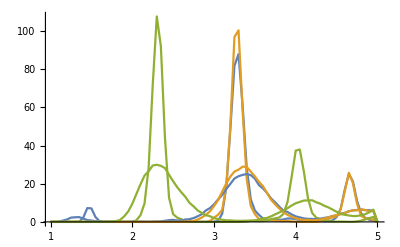

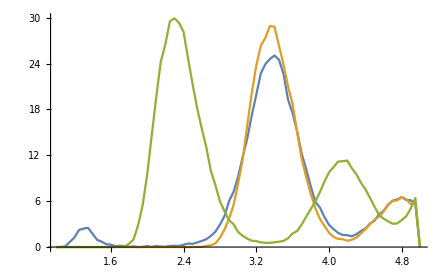

```mathematica
Show[{ListLinePlot[{plotCC2,plotZrZr2,plotZrC2},PlotRange->All],ListLinePlot@{plotCC,plotZrZr,plotZrC}}]
```

```mathematica
pairCorrlation=ListLinePlot@{plotCC,plotZrZr,plotZrC};
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/pairCorrlation.pdf",pairCorrlation]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/pairCorrlation.pdf

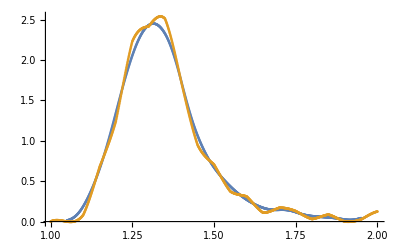

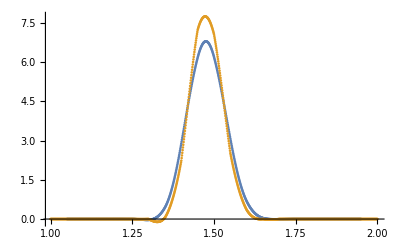

```mathematica
cdat=Table[{x,Interpolation[plotCC][x]},{x,1,2,0.001}];
meancdat=MovingMap[Mean,cdat,{0.1,Center}];
ListPlot[{meancdat,cdat},PlotRange->All]
cdat2=Table[{x,Interpolation[plotCC2][x]},{x,1,2,0.001}];
meancdat2=MovingMap[Mean,cdat2,{0.1,Center}];
ListPlot[{meancdat2,cdat2},PlotRange->All]
```

```mathematica
Maximize[Interpolation[cdat][x]&&x<2,{x}]
Maximize[Interpolation[meancdat][x]&&x<2,{x}]
```

InterpolatingFunction::dmval: Input value {-0.829053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.969346} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.912378} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{2.53925,{x→1.3363}}

InterpolatingFunction::dmval: Input value {-0.829053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.969346} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.912378} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{2.45084,{x→1.31435}}

```mathematica
Maximize[Interpolation[cdat2][x],{x}]
Maximize[Interpolation[meancdat2][x],{x}]
```

InterpolatingFunction::dmval: Input value {-0.829053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.969346} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.912378} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{7.75531,{x→1.47294}}

InterpolatingFunction::dmval: Input value {-0.829053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.969346} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.912378} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{6.80211,{x→1.47523}}